```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.53;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-3.56587},{0.01,-3.44356},{0.02,-3.32935},{0.03,-3.22259},{0.04,-3.12267},{0.05,-3.02903},{0.06,-2.94112},{0.07,-2.8585},{0.08,-2.78073},{0.09,-2.70741},{0.1,-2.63818},{0.11,-2.5727},{0.12,-2.51069},{0.13,-2.45187},{0.14,-2.39597},{0.15,-2.34283},{0.16,-2.29221},{0.17,-2.24391},{0.18,-2.19776},{0.19,-2.15366},{0.2,-2.11142},{0.21,-2.0709},{0.22,-2.03204},{0.23,-1.99467},{0.24,-1.95875},{0.25,-1.92415},{0.26,-1.89079},{0.27,-1.85862},{0.28,-1.82755},{0.29,-1.79752},{0.3,-1.76846},{0.31,-1.74034},{0.32,-1.71309},{0.33,-1.68666},{0.34,-1.66103},{0.35,-1.63613},{0.36,-1.61195},{0.37,-1.58843},{0.38,-1.56557},{0.39,-1.5433},{0.4,-1.52159},{0.41,-1.50047},{0.42,-1.47989},{0.43,-1.45978},{0.44,-1.44016},{0.45,-1.42104},{0.46,-1.40234},{0.47,-1.38405},{0.48,-1.36619},{0.49,-1.34874},{0.5,-1.33165},{0.51,-1.31491},{0.52,-1.29854},{0.53,-1.28252},{0.54,-1.26682},{0.55,-1.25142},{0.56,-1.23632},{0.57,-1.22154},{0.58,-1.20704},{0.59,-1.1928},{0.6,-1.17882},{0.61,-1.16511},{0.62,-1.15167},{0.63,-1.13845},{0.64,-1.12545},{0.65,-1.11269},{0.66,-1.10015},{0.67,-1.08785},{0.68,-1.07573},{0.69,-1.06381},{0.7,-1.05208},{0.71,-1.04056},{0.72,-1.02924},{0.73,-1.01808},{0.74,-1.00709},{0.75,-0.996273},{0.76,-0.985627},{0.77,-0.975162},{0.78,-0.964888},{0.79,-0.954736},{0.8,-0.944711},{0.81,-0.934819},{0.82,-0.925063},{0.83,-0.915447},{0.84,-0.905976},{0.85,-0.896652},{0.86,-0.887479},{0.87,-0.87846},{0.88,-0.869561},{0.89,-0.860757},{0.9,-0.852062},{0.91,-0.843481},{0.92,-0.835018},{0.93,-0.826678},{0.94,-0.81846},{0.95,-0.810337},{0.96,-0.802307},{0.97,-0.794377},{0.98,-0.786549},{0.99,-0.778828},{1.,-0.771217}}

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gammap004n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-2.03702},{0.01,-2.05031},{0.02,-2.06452},{0.03,-2.07966},{0.04,-2.09577},{0.05,-2.1129},{0.06,-2.13106},{0.07,-2.15032},{0.08,-2.17069},{0.09,-2.19224},{0.1,-2.21501},{0.11,-2.23904},{0.12,-2.26439},{0.13,-2.29112},{0.14,-2.31928},{0.15,-2.34894},{0.16,-2.38016},{0.17,-2.41303},{0.18,-2.4476},{0.19,-2.48398},{0.2,-2.52223},{0.21,-2.56249},{0.22,-2.6048},{0.23,-2.64934},{0.24,-2.69617},{0.25,-2.74545},{0.26,-2.79732},{0.27,-2.85189},{0.28,-2.90941},{0.29,-2.96996},{0.3,-3.03378},{0.31,-3.10111},{0.32,-3.17209},{0.33,-3.24709},{0.34,-3.3263},{0.35,-3.41},{0.36,-3.49868},{0.37,-3.59253},{0.38,-3.69199},{0.39,-3.79771},{0.4,-3.90994},{0.41,-4.0293},{0.42,-4.15662},{0.43,-4.29242},{0.44,-4.43757},{0.45,-4.59299},{0.46,-4.75972},{0.47,-4.93894},{0.48,-5.13202},{0.49,-5.34056},{0.5,-5.56636},{0.51,-5.81158},{0.52,-6.07873},{0.53,-6.37074},{0.54,-6.69118},{0.55,-7.04426},{0.56,-7.43512},{0.57,-7.87},{0.58,-8.35665},{0.59,-8.90476},{0.6,-9.52659},{0.61,-10.2379},{0.62,-11.0592},{0.63,-12.0181},{0.64,-13.152},{0.65,-14.5133},{0.66,-16.1778},{0.67,-18.259},{0.68,-20.9356},{0.69,-24.5058},{0.7,-29.5048},{0.71,-37.0014},{0.72,-49.5037},{0.73,-74.4982},{0.74,-149.511},{0.75,-1638.29},{0.76,150.473},{0.77,75.5007},{0.78,50.501},{0.79,38.0021},{0.8,30.5032},{0.81,25.5031},{0.82,21.932},{0.83,19.2541},{0.84,17.1717},{0.85,15.5057},{0.86,14.143},{0.87,13.0075},{0.88,12.0468},{0.89,11.2235},{0.9,10.5101},{0.91,9.88606},{0.92,9.33559},{0.93,8.84638},{0.94,8.40867},{0.95,8.01479},{0.96,7.65877},{0.97,7.33481},{0.98,7.03951},{0.99,6.76855},{1.,6.5195}}

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gammap004n=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-2.41923},{0.01,-2.40901},{0.02,-2.3997},{0.03,-2.39129},{0.04,-2.38379},{0.05,-2.37718},{0.06,-2.37148},{0.07,-2.36668},{0.08,-2.36276},{0.09,-2.35973},{0.1,-2.35756},{0.11,-2.35628},{0.12,-2.35585},{0.13,-2.35628},{0.14,-2.35755},{0.15,-2.35965},{0.16,-2.36259},{0.17,-2.36634},{0.18,-2.37093},{0.19,-2.37628},{0.2,-2.38243},{0.21,-2.38941},{0.22,-2.39714},{0.23,-2.40562},{0.24,-2.4149},{0.25,-2.42496},{0.26,-2.43574},{0.27,-2.44726},{0.28,-2.45956},{0.29,-2.47262},{0.3,-2.48637},{0.31,-2.50085},{0.32,-2.5161},{0.33,-2.5321},{0.34,-2.54879},{0.35,-2.5662},{0.36,-2.58437},{0.37,-2.60332},{0.38,-2.62296},{0.39,-2.64331},{0.4,-2.66441},{0.41,-2.6863},{0.42,-2.70895},{0.43,-2.73231},{0.44,-2.75642},{0.45,-2.78132},{0.46,-2.80704},{0.47,-2.83354},{0.48,-2.8608},{0.49,-2.88888},{0.5,-2.9178},{0.51,-2.94757},{0.52,-2.97816},{0.53,-3.00961},{0.54,-3.04194},{0.55,-3.07521},{0.56,-3.10937},{0.57,-3.14446},{0.58,-3.1805},{0.59,-3.21753},{0.6,-3.25559},{0.61,-3.29465},{0.62,-3.33477},{0.63,-3.37596},{0.64,-3.41829},{0.65,-3.46176},{0.66,-3.50641},{0.67,-3.55227},{0.68,-3.59938},{0.69,-3.64778},{0.7,-3.69752},{0.71,-3.74863},{0.72,-3.80119},{0.73,-3.85522},{0.74,-3.91076},{0.75,-3.96787},{0.76,-4.02665},{0.77,-4.08716},{0.78,-4.14943},{0.79,-4.2135},{0.8,-4.27946},{0.81,-4.34748},{0.82,-4.41762},{0.83,-4.48991},{0.84,-4.56439},{0.85,-4.64114},{0.86,-4.72049},{0.87,-4.80251},{0.88,-4.88724},{0.89,-4.97472},{0.9,-5.06501},{0.91,-5.15856},{0.92,-5.25547},{0.93,-5.3558},{0.94,-5.45962},{0.95,-5.56737},{0.96,-5.6792},{0.97,-5.79517},{0.98,-5.9157},{0.99,-6.04109},{1.,-6.1714}}

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gammap004n=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-3.18366},{0.01,-3.10545},{0.02,-3.03144},{0.03,-2.9614},{0.04,-2.89508},{0.05,-2.83225},{0.06,-2.77269},{0.07,-2.71619},{0.08,-2.66255},{0.09,-2.61159},{0.1,-2.56314},{0.11,-2.51703},{0.12,-2.47309},{0.13,-2.43118},{0.14,-2.39117},{0.15,-2.35295},{0.16,-2.3164},{0.17,-2.28137},{0.18,-2.24784},{0.19,-2.21563},{0.2,-2.18472},{0.21,-2.155},{0.22,-2.12639},{0.23,-2.09885},{0.24,-2.07227},{0.25,-2.04665},{0.26,-2.02188},{0.27,-1.99794},{0.28,-1.97477},{0.29,-1.95233},{0.3,-1.93059},{0.31,-1.90948},{0.32,-1.88902},{0.33,-1.86911},{0.34,-1.84976},{0.35,-1.83095},{0.36,-1.81262},{0.37,-1.79476},{0.38,-1.77737},{0.39,-1.76038},{0.4,-1.7438},{0.41,-1.72763},{0.42,-1.7118},{0.43,-1.69633},{0.44,-1.68121},{0.45,-1.6664},{0.46,-1.65189},{0.47,-1.6377},{0.48,-1.62378},{0.49,-1.61012},{0.5,-1.59673},{0.51,-1.5836},{0.52,-1.5707},{0.53,-1.55803},{0.54,-1.54559},{0.55,-1.53338},{0.56,-1.52134},{0.57,-1.50951},{0.58,-1.49787},{0.59,-1.48642},{0.6,-1.47518},{0.61,-1.4641},{0.62,-1.45317},{0.63,-1.4424},{0.64,-1.43179},{0.65,-1.42134},{0.66,-1.41106},{0.67,-1.40092},{0.68,-1.39091},{0.69,-1.38102},{0.7,-1.37127},{0.71,-1.36164},{0.72,-1.35215},{0.73,-1.3428},{0.74,-1.33356},{0.75,-1.32443},{0.76,-1.3154},{0.77,-1.30648},{0.78,-1.29767},{0.79,-1.28897},{0.8,-1.28038},{0.81,-1.2719},{0.82,-1.2635},{0.83,-1.2552},{0.84,-1.24698},{0.85,-1.23885},{0.86,-1.23081},{0.87,-1.22287},{0.88,-1.21502},{0.89,-1.20725},{0.9,-1.19957},{0.91,-1.19195},{0.92,-1.18442},{0.93,-1.17696},{0.94,-1.16958},{0.95,-1.16228},{0.96,-1.15505},{0.97,-1.14789},{0.98,-1.14079},{0.99,-1.13377},{1.,-1.12682}}

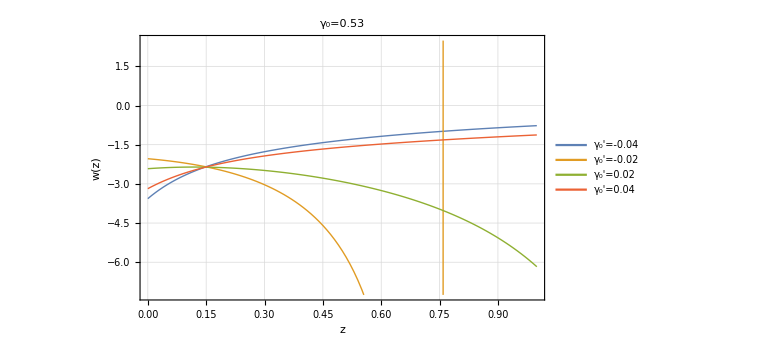

```mathematica
list=ListLinePlot[{points1,points2,points3, points4}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_0'=-0.04", "γ_0'=-0.02", "γ_0'=0.02", "γ_0'=0.04"},LegendFunction->"Frame", Background->White],{Right,Bottom}], GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["γ_0=0.53", Black, FontSize->20]]
```

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.55;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.82211},{0.01,-1.78217},{0.02,-1.74385},{0.03,-1.70707},{0.04,-1.67173},{0.05,-1.63776},{0.06,-1.60509},{0.07,-1.57363},{0.08,-1.54334},{0.09,-1.51415},{0.1,-1.48599},{0.11,-1.45882},{0.12,-1.43259},{0.13,-1.40724},{0.14,-1.38274},{0.15,-1.35902},{0.16,-1.33608},{0.17,-1.31384},{0.18,-1.29231},{0.19,-1.27142},{0.2,-1.25115},{0.21,-1.23149},{0.22,-1.21238},{0.23,-1.19382},{0.24,-1.17577},{0.25,-1.15821},{0.26,-1.14114},{0.27,-1.1245},{0.28,-1.1083},{0.29,-1.09252},{0.3,-1.07712},{0.31,-1.06211},{0.32,-1.04749},{0.33,-1.0332},{0.34,-1.01922},{0.35,-1.00555},{0.36,-0.992206},{0.37,-0.979188},{0.38,-0.966481},{0.39,-0.95402},{0.4,-0.94181},{0.41,-0.929856},{0.42,-0.918163},{0.43,-0.906732},{0.44,-0.895516},{0.45,-0.884505},{0.46,-0.873706},{0.47,-0.863125},{0.48,-0.852766},{0.49,-0.842599},{0.5,-0.832604},{0.51,-0.822788},{0.52,-0.813158},{0.53,-0.803715},{0.54,-0.794425},{0.55,-0.785285},{0.56,-0.776305},{0.57,-0.76749},{0.58,-0.758832},{0.59,-0.750299},{0.6,-0.741898},{0.61,-0.733637},{0.62,-0.725521},{0.63,-0.717543},{0.64,-0.709672},{0.65,-0.701913},{0.66,-0.694273},{0.67,-0.68676},{0.68,-0.679375},{0.69,-0.672084},{0.7,-0.66489},{0.71,-0.657801},{0.72,-0.650825},{0.73,-0.643957},{0.74,-0.63717},{0.75,-0.63047},{0.76,-0.623865},{0.77,-0.617363},{0.78,-0.610957},{0.79,-0.60462},{0.8,-0.59836},{0.81,-0.592183},{0.82,-0.586098},{0.83,-0.580106},{0.84,-0.574175},{0.85,-0.568308},{0.86,-0.562513},{0.87,-0.556798},{0.88,-0.551169},{0.89,-0.545611},{0.9,-0.540103},{0.91,-0.534653},{0.92,-0.529269},{0.93,-0.523959},{0.94,-0.518728},{0.95,-0.513548},{0.96,-0.508416},{0.97,-0.50334},{0.98,-0.498328},{0.99,-0.493384},{1.,-0.488487}}

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gammap004n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-0.904793},{0.01,-0.908795},{0.02,-0.913012},{0.03,-0.917438},{0.04,-0.922077},{0.05,-0.92693},{0.06,-0.932001},{0.07,-0.93729},{0.08,-0.942802},{0.09,-0.948537},{0.1,-0.954497},{0.11,-0.960693},{0.12,-0.967113},{0.13,-0.973778},{0.14,-0.980676},{0.15,-0.987825},{0.16,-0.995215},{0.17,-1.00286},{0.18,-1.01076},{0.19,-1.01893},{0.2,-1.02736},{0.21,-1.03606},{0.22,-1.04505},{0.23,-1.0543},{0.24,-1.06386},{0.25,-1.07373},{0.26,-1.08387},{0.27,-1.09433},{0.28,-1.10513},{0.29,-1.11624},{0.3,-1.12767},{0.31,-1.13946},{0.32,-1.15162},{0.33,-1.16412},{0.34,-1.17698},{0.35,-1.19024},{0.36,-1.20391},{0.37,-1.21798},{0.38,-1.23243},{0.39,-1.24735},{0.4,-1.26272},{0.41,-1.27854},{0.42,-1.29482},{0.43,-1.31161},{0.44,-1.3289},{0.45,-1.34671},{0.46,-1.36507},{0.47,-1.38399},{0.48,-1.4035},{0.49,-1.42361},{0.5,-1.44434},{0.51,-1.46574},{0.52,-1.4878},{0.53,-1.51058},{0.54,-1.53408},{0.55,-1.55836},{0.56,-1.58342},{0.57,-1.60932},{0.58,-1.63608},{0.59,-1.66374},{0.6,-1.69235},{0.61,-1.72195},{0.62,-1.75258},{0.63,-1.78429},{0.64,-1.81713},{0.65,-1.85117},{0.66,-1.88645},{0.67,-1.92305},{0.68,-1.96103},{0.69,-2.00046},{0.7,-2.04143},{0.71,-2.084},{0.72,-2.12829},{0.73,-2.17438},{0.74,-2.22238},{0.75,-2.27241},{0.76,-2.32458},{0.77,-2.37903},{0.78,-2.4359},{0.79,-2.49535},{0.8,-2.55755},{0.81,-2.6227},{0.82,-2.69099},{0.83,-2.76263},{0.84,-2.8379},{0.85,-2.91704},{0.86,-3.00037},{0.87,-3.0882},{0.88,-3.1809},{0.89,-3.27889},{0.9,-3.38258},{0.91,-3.49255},{0.92,-3.60927},{0.93,-3.73347},{0.94,-3.86578},{0.95,-4.0071},{0.96,-4.15828},{0.97,-4.32045},{0.98,-4.49476},{0.99,-4.68266},{1.,-4.88576}}

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gammap004n=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.13412},{0.01,-1.13104},{0.02,-1.12818},{0.03,-1.12552},{0.04,-1.12307},{0.05,-1.12082},{0.06,-1.11877},{0.07,-1.11691},{0.08,-1.11524},{0.09,-1.11375},{0.1,-1.11245},{0.11,-1.11132},{0.12,-1.11038},{0.13,-1.1096},{0.14,-1.109},{0.15,-1.10856},{0.16,-1.10829},{0.17,-1.10818},{0.18,-1.10823},{0.19,-1.10844},{0.2,-1.1088},{0.21,-1.10932},{0.22,-1.10999},{0.23,-1.11081},{0.24,-1.11178},{0.25,-1.11288},{0.26,-1.11414},{0.27,-1.11554},{0.28,-1.11708},{0.29,-1.11876},{0.3,-1.12058},{0.31,-1.12253},{0.32,-1.12462},{0.33,-1.12685},{0.34,-1.12921},{0.35,-1.1317},{0.36,-1.13431},{0.37,-1.13707},{0.38,-1.13996},{0.39,-1.14298},{0.4,-1.14611},{0.41,-1.14938},{0.42,-1.15279},{0.43,-1.15632},{0.44,-1.15997},{0.45,-1.16374},{0.46,-1.16765},{0.47,-1.17169},{0.48,-1.17586},{0.49,-1.18014},{0.5,-1.18454},{0.51,-1.18908},{0.52,-1.19374},{0.53,-1.19854},{0.54,-1.20346},{0.55,-1.20849},{0.56,-1.21365},{0.57,-1.21895},{0.58,-1.22438},{0.59,-1.22993},{0.6,-1.23561},{0.61,-1.24141},{0.62,-1.24734},{0.63,-1.25341},{0.64,-1.25961},{0.65,-1.26595},{0.66,-1.27241},{0.67,-1.279},{0.68,-1.28572},{0.69,-1.29259},{0.7,-1.29959},{0.71,-1.30672},{0.72,-1.31399},{0.73,-1.32141},{0.74,-1.32896},{0.75,-1.33665},{0.76,-1.34449},{0.77,-1.35247},{0.78,-1.3606},{0.79,-1.36887},{0.8,-1.37729},{0.81,-1.38587},{0.82,-1.3946},{0.83,-1.40348},{0.84,-1.41251},{0.85,-1.4217},{0.86,-1.43106},{0.87,-1.44057},{0.88,-1.45025},{0.89,-1.46009},{0.9,-1.4701},{0.91,-1.48029},{0.92,-1.49064},{0.93,-1.50117},{0.94,-1.51188},{0.95,-1.52277},{0.96,-1.53384},{0.97,-1.5451},{0.98,-1.55655},{0.99,-1.56818},{1.,-1.58002}}

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gammap004n=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.59278},{0.01,-1.56769},{0.02,-1.54344},{0.03,-1.52},{0.04,-1.49732},{0.05,-1.47539},{0.06,-1.45415},{0.07,-1.4336},{0.08,-1.41367},{0.09,-1.39437},{0.1,-1.37565},{0.11,-1.3575},{0.12,-1.33988},{0.13,-1.32278},{0.14,-1.30617},{0.15,-1.29003},{0.16,-1.27434},{0.17,-1.25908},{0.18,-1.24424},{0.19,-1.22979},{0.2,-1.21573},{0.21,-1.20202},{0.22,-1.18866},{0.23,-1.17563},{0.24,-1.16295},{0.25,-1.15056},{0.26,-1.13846},{0.27,-1.12665},{0.28,-1.11513},{0.29,-1.10386},{0.3,-1.09284},{0.31,-1.08206},{0.32,-1.07154},{0.33,-1.06122},{0.34,-1.05113},{0.35,-1.04124},{0.36,-1.03157},{0.37,-1.02209},{0.38,-1.01278},{0.39,-1.00367},{0.4,-0.994734},{0.41,-0.985972},{0.42,-0.977362},{0.43,-0.968909},{0.44,-0.960615},{0.45,-0.95248},{0.46,-0.944482},{0.47,-0.936614},{0.48,-0.928879},{0.49,-0.92128},{0.5,-0.91382},{0.51,-0.906475},{0.52,-0.89924},{0.53,-0.892117},{0.54,-0.88511},{0.55,-0.878222},{0.56,-0.871444},{0.57,-0.864755},{0.58,-0.85816},{0.59,-0.851661},{0.6,-0.845262},{0.61,-0.838967},{0.62,-0.832756},{0.63,-0.826623},{0.64,-0.82057},{0.65,-0.814603},{0.66,-0.808725},{0.67,-0.802927},{0.68,-0.797194},{0.69,-0.791531},{0.7,-0.785941},{0.71,-0.780429},{0.72,-0.774996},{0.73,-0.76962},{0.74,-0.764301},{0.75,-0.759045},{0.76,-0.753854},{0.77,-0.748733},{0.78,-0.74368},{0.79,-0.738673},{0.8,-0.733716},{0.81,-0.728812},{0.82,-0.723965},{0.83,-0.719181},{0.84,-0.714457},{0.85,-0.709775},{0.86,-0.705135},{0.87,-0.700543},{0.88,-0.696003},{0.89,-0.691519},{0.9,-0.68708},{0.91,-0.682678},{0.92,-0.678317},{0.93,-0.674},{0.94,-0.669733},{0.95,-0.665514},{0.96,-0.661327},{0.97,-0.657175},{0.98,-0.653061},{0.99,-0.64899},{1.,-0.644966}}

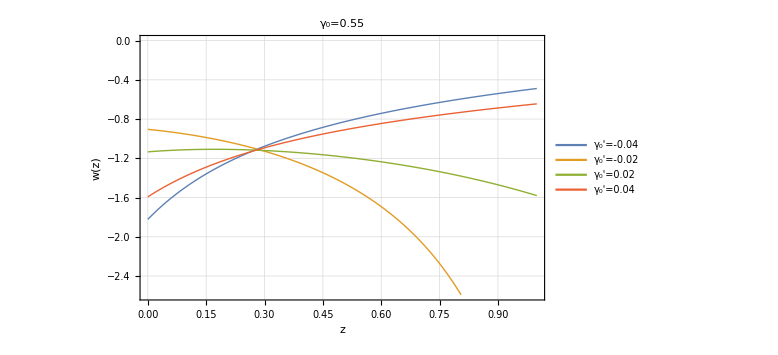

```mathematica
list2=ListLinePlot[{points1,points2,points3, points4}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_0'=-0.04", "γ_0'=-0.02", "γ_0'=0.02", "γ_0'=0.04"},LegendFunction->"Frame", Background->White],{Right,Bottom}], GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["γ_0=0.55", Black, FontSize->20]]
```

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.57;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-1.07337},{0.01,-1.05551},{0.02,-1.03816},{0.03,-1.02132},{0.04,-1.00495},{0.05,-0.989032},{0.06,-0.973555},{0.07,-0.958498},{0.08,-0.943841},{0.09,-0.929572},{0.1,-0.915668},{0.11,-0.902126},{0.12,-0.888917},{0.13,-0.876044},{0.14,-0.863478},{0.15,-0.851222},{0.16,-0.839251},{0.17,-0.827564},{0.18,-0.816147},{0.19,-0.804986},{0.2,-0.794084},{0.21,-0.783414},{0.22,-0.772983},{0.23,-0.762777},{0.24,-0.752779},{0.25,-0.743003},{0.26,-0.733426},{0.27,-0.724034},{0.28,-0.714842},{0.29,-0.705836},{0.3,-0.696992},{0.31,-0.688326},{0.32,-0.679838},{0.33,-0.671494},{0.34,-0.663303},{0.35,-0.655279},{0.36,-0.647396},{0.37,-0.639642},{0.38,-0.632031},{0.39,-0.62457},{0.4,-0.617222},{0.41,-0.609992},{0.42,-0.602894},{0.43,-0.59593},{0.44,-0.589063},{0.45,-0.5823},{0.46,-0.575656},{0.47,-0.569137},{0.48,-0.562702},{0.49,-0.556357},{0.5,-0.550116},{0.51,-0.543991},{0.52,-0.537952},{0.53,-0.531985},{0.54,-0.526105},{0.55,-0.520325},{0.56,-0.514643},{0.57,-0.509023},{0.58,-0.503477},{0.59,-0.498017},{0.6,-0.492649},{0.61,-0.487339},{0.62,-0.482093},{0.63,-0.476924},{0.64,-0.471842},{0.65,-0.466818},{0.66,-0.461846},{0.67,-0.456941},{0.68,-0.452113},{0.69,-0.447356},{0.7,-0.442641},{0.71,-0.437976},{0.72,-0.433377},{0.73,-0.428853},{0.74,-0.424384},{0.75,-0.419949},{0.76,-0.415562},{0.77,-0.411236},{0.78,-0.40698},{0.79,-0.402768},{0.8,-0.398591},{0.81,-0.39446},{0.82,-0.390388},{0.83,-0.386373},{0.84,-0.382388},{0.85,-0.37844},{0.86,-0.37454},{0.87,-0.3707},{0.88,-0.366901},{0.89,-0.363127},{0.9,-0.359389},{0.91,-0.3557},{0.92,-0.352065},{0.93,-0.348459},{0.94,-0.344882},{0.95,-0.341344},{0.96,-0.337856},{0.97,-0.334398},{0.98,-0.330966},{0.99,-0.32757},{1.,-0.32422}}

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gammap004n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-0.418146},{0.01,-0.420016},{0.02,-0.421953},{0.03,-0.423956},{0.04,-0.426025},{0.05,-0.428161},{0.06,-0.430364},{0.07,-0.432635},{0.08,-0.434974},{0.09,-0.43738},{0.1,-0.439855},{0.11,-0.442399},{0.12,-0.445013},{0.13,-0.447696},{0.14,-0.450451},{0.15,-0.453275},{0.16,-0.456173},{0.17,-0.459142},{0.18,-0.462185},{0.19,-0.465304},{0.2,-0.468493},{0.21,-0.471764},{0.22,-0.475105},{0.23,-0.478528},{0.24,-0.482031},{0.25,-0.485607},{0.26,-0.489271},{0.27,-0.493015},{0.28,-0.496837},{0.29,-0.50075},{0.3,-0.504742},{0.31,-0.508827},{0.32,-0.512997},{0.33,-0.517256},{0.34,-0.52161},{0.35,-0.526049},{0.36,-0.53059},{0.37,-0.535225},{0.38,-0.539951},{0.39,-0.544787},{0.4,-0.549715},{0.41,-0.554748},{0.42,-0.559893},{0.43,-0.565134},{0.44,-0.570492},{0.45,-0.57596},{0.46,-0.581537},{0.47,-0.587238},{0.48,-0.593047},{0.49,-0.598985},{0.5,-0.605046},{0.51,-0.611225},{0.52,-0.617544},{0.53,-0.623986},{0.54,-0.630564},{0.55,-0.637288},{0.56,-0.644139},{0.57,-0.651144},{0.58,-0.658301},{0.59,-0.665593},{0.6,-0.673054},{0.61,-0.680676},{0.62,-0.688446},{0.63,-0.696395},{0.64,-0.704512},{0.65,-0.7128},{0.66,-0.721279},{0.67,-0.729929},{0.68,-0.738779},{0.69,-0.747826},{0.7,-0.75706},{0.71,-0.766515},{0.72,-0.776177},{0.73,-0.786048},{0.74,-0.796158},{0.75,-0.80649},{0.76,-0.817054},{0.77,-0.827878},{0.78,-0.838942},{0.79,-0.850261},{0.8,-0.861865},{0.81,-0.873733},{0.82,-0.885878},{0.83,-0.898336},{0.84,-0.91109},{0.85,-0.92414},{0.86,-0.937536},{0.87,-0.951266},{0.88,-0.965321},{0.89,-0.97975},{0.9,-0.994551},{0.91,-1.00972},{0.92,-1.0253},{0.93,-1.04129},{0.94,-1.05769},{0.95,-1.07455},{0.96,-1.09187},{0.97,-1.10965},{0.98,-1.12794},{0.99,-1.14673},{1.,-1.16607}}

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gammap004n=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-0.581952},{0.01,-0.580919},{0.02,-0.579951},{0.03,-0.579055},{0.04,-0.578226},{0.05,-0.577463},{0.06,-0.576764},{0.07,-0.576129},{0.08,-0.575556},{0.09,-0.575043},{0.1,-0.574589},{0.11,-0.574196},{0.12,-0.573856},{0.13,-0.573575},{0.14,-0.573351},{0.15,-0.573177},{0.16,-0.573058},{0.17,-0.572994},{0.18,-0.572979},{0.19,-0.573014},{0.2,-0.573102},{0.21,-0.573237},{0.22,-0.57342},{0.23,-0.573652},{0.24,-0.573933},{0.25,-0.574258},{0.26,-0.574629},{0.27,-0.575047},{0.28,-0.575509},{0.29,-0.576015},{0.3,-0.576565},{0.31,-0.577158},{0.32,-0.577795},{0.33,-0.578473},{0.34,-0.579194},{0.35,-0.579956},{0.36,-0.58076},{0.37,-0.581604},{0.38,-0.582487},{0.39,-0.583412},{0.4,-0.584378},{0.41,-0.585381},{0.42,-0.586423},{0.43,-0.587506},{0.44,-0.588627},{0.45,-0.589786},{0.46,-0.590984},{0.47,-0.59222},{0.48,-0.593493},{0.49,-0.594803},{0.5,-0.596152},{0.51,-0.597539},{0.52,-0.59896},{0.53,-0.60042},{0.54,-0.601918},{0.55,-0.603452},{0.56,-0.605019},{0.57,-0.606627},{0.58,-0.608272},{0.59,-0.609952},{0.6,-0.611666},{0.61,-0.613419},{0.62,-0.615209},{0.63,-0.617032},{0.64,-0.618893},{0.65,-0.620792},{0.66,-0.622726},{0.67,-0.624693},{0.68,-0.6267},{0.69,-0.628745},{0.7,-0.630823},{0.71,-0.632935},{0.72,-0.635088},{0.73,-0.637279},{0.74,-0.639501},{0.75,-0.64176},{0.76,-0.64406},{0.77,-0.646397},{0.78,-0.648767},{0.79,-0.651172},{0.8,-0.65362},{0.81,-0.656106},{0.82,-0.658626},{0.83,-0.66118},{0.84,-0.663777},{0.85,-0.666412},{0.86,-0.669083},{0.87,-0.67179},{0.88,-0.674541},{0.89,-0.67733},{0.9,-0.680152},{0.91,-0.683016},{0.92,-0.685923},{0.93,-0.688868},{0.94,-0.691847},{0.95,-0.694871},{0.96,-0.697936},{0.97,-0.701038},{0.98,-0.704182},{0.99,-0.70737},{1.,-0.710596}}

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gammap004n=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-0.909563},{0.01,-0.898647},{0.02,-0.887995},{0.03,-0.877602},{0.04,-0.867458},{0.05,-0.857554},{0.06,-0.847879},{0.07,-0.838427},{0.08,-0.82919},{0.09,-0.820159},{0.1,-0.811328},{0.11,-0.802691},{0.12,-0.794237},{0.13,-0.785965},{0.14,-0.777867},{0.15,-0.769933},{0.16,-0.762166},{0.17,-0.754549},{0.18,-0.747091},{0.19,-0.739774},{0.2,-0.7326},{0.21,-0.725567},{0.22,-0.718659},{0.23,-0.711889},{0.24,-0.705237},{0.25,-0.698705},{0.26,-0.6923},{0.27,-0.685997},{0.28,-0.679805},{0.29,-0.673731},{0.3,-0.667751},{0.31,-0.661868},{0.32,-0.656092},{0.33,-0.650412},{0.34,-0.644812},{0.35,-0.639307},{0.36,-0.633901},{0.37,-0.628567},{0.38,-0.62331},{0.39,-0.618144},{0.4,-0.613062},{0.41,-0.608041},{0.42,-0.603092},{0.43,-0.598227},{0.44,-0.593437},{0.45,-0.588699},{0.46,-0.584027},{0.47,-0.579429},{0.48,-0.574904},{0.49,-0.570425},{0.5,-0.566},{0.51,-0.561641},{0.52,-0.557355},{0.53,-0.553114},{0.54,-0.548916},{0.55,-0.544772},{0.56,-0.540691},{0.57,-0.536673},{0.58,-0.532688},{0.59,-0.528742},{0.6,-0.524846},{0.61,-0.52101},{0.62,-0.517226},{0.63,-0.513471},{0.64,-0.509755},{0.65,-0.506087},{0.66,-0.502474},{0.67,-0.498892},{0.68,-0.49534},{0.69,-0.491828},{0.7,-0.488365},{0.71,-0.484948},{0.72,-0.481553},{0.73,-0.478186},{0.74,-0.474859},{0.75,-0.471578},{0.76,-0.468337},{0.77,-0.465113},{0.78,-0.461916},{0.79,-0.458753},{0.8,-0.455634},{0.81,-0.452555},{0.82,-0.449491},{0.83,-0.446447},{0.84,-0.443432},{0.85,-0.440455},{0.86,-0.437521},{0.87,-0.434604},{0.88,-0.431704},{0.89,-0.428829},{0.9,-0.425988},{0.91,-0.423183},{0.92,-0.420393},{0.93,-0.417621},{0.94,-0.414875},{0.95,-0.412162},{0.96,-0.409478},{0.97,-0.406804},{0.98,-0.404149},{0.99,-0.40152},{1.,-0.398924}}

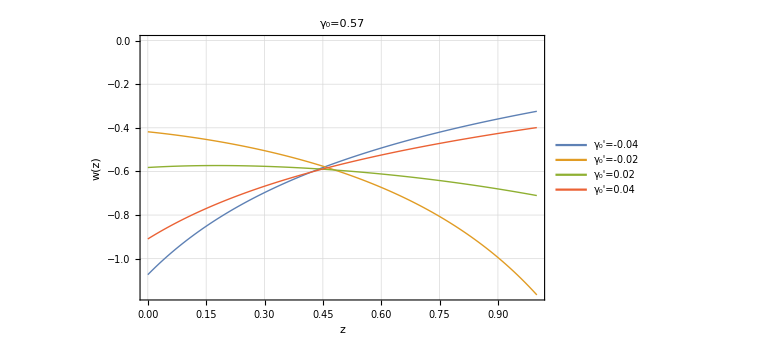

```mathematica
list3=ListLinePlot[{points1,points2,points3, points4}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_0'=-0.04", "γ_0'=-0.02", "γ_0'=0.02", "γ_0'=0.04"},LegendFunction->"Frame", Background->White],{Right,Bottom}], GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["γ_0=0.57", Black, FontSize->20]]
```

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.59;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-0.656207},{0.01,-0.647088},{0.02,-0.638174},{0.03,-0.629458},{0.04,-0.620933},{0.05,-0.612591},{0.06,-0.604427},{0.07,-0.596434},{0.08,-0.588609},{0.09,-0.580939},{0.1,-0.57343},{0.11,-0.566065},{0.12,-0.55885},{0.13,-0.55177},{0.14,-0.544831},{0.15,-0.538018},{0.16,-0.531339},{0.17,-0.524776},{0.18,-0.518341},{0.19,-0.512013},{0.2,-0.505809},{0.21,-0.499703},{0.22,-0.493704},{0.23,-0.487821},{0.24,-0.482021},{0.25,-0.476326},{0.26,-0.470734},{0.27,-0.465216},{0.28,-0.459798},{0.29,-0.454475},{0.3,-0.449218},{0.31,-0.444052},{0.32,-0.438979},{0.33,-0.433963},{0.34,-0.429027},{0.35,-0.424185},{0.36,-0.419396},{0.37,-0.414672},{0.38,-0.410035},{0.39,-0.405465},{0.4,-0.40094},{0.41,-0.396486},{0.42,-0.392117},{0.43,-0.387789},{0.44,-0.38351},{0.45,-0.379301},{0.46,-0.375168},{0.47,-0.371066},{0.48,-0.367011},{0.49,-0.363021},{0.5,-0.359105},{0.51,-0.355214},{0.52,-0.351362},{0.53,-0.347569},{0.54,-0.343849},{0.55,-0.340158},{0.56,-0.336495},{0.57,-0.332878},{0.58,-0.329325},{0.59,-0.325822},{0.6,-0.322338},{0.61,-0.318894},{0.62,-0.315506},{0.63,-0.312161},{0.64,-0.308834},{0.65,-0.305546},{0.66,-0.302312},{0.67,-0.299119},{0.68,-0.295941},{0.69,-0.292795},{0.7,-0.289698},{0.71,-0.286649},{0.72,-0.283612},{0.73,-0.280599},{0.74,-0.277626},{0.75,-0.274706},{0.76,-0.271807},{0.77,-0.26892},{0.78,-0.266062},{0.79,-0.263247},{0.8,-0.260481},{0.81,-0.257722},{0.82,-0.254977},{0.83,-0.252261},{0.84,-0.249588},{0.85,-0.246955},{0.86,-0.244328},{0.87,-0.241719},{0.88,-0.239142},{0.89,-0.236607},{0.9,-0.234085},{0.91,-0.231575},{0.92,-0.22909},{0.93,-0.226643},{0.94,-0.224219},{0.95,-0.221807},{0.96,-0.219418},{0.97,-0.217062},{0.98,-0.214717},{0.99,-0.21239},{1.,-0.210094}}

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gammap004n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-0.146589},{0.01,-0.14774},{0.02,-0.148912},{0.03,-0.150104},{0.04,-0.151315},{0.05,-0.152545},{0.06,-0.153796},{0.07,-0.155069},{0.08,-0.156358},{0.09,-0.157674},{0.1,-0.159003},{0.11,-0.160361},{0.12,-0.161732},{0.13,-0.163133},{0.14,-0.164547},{0.15,-0.165992},{0.16,-0.167448},{0.17,-0.168938},{0.18,-0.17044},{0.19,-0.171972},{0.2,-0.17353},{0.21,-0.175094},{0.22,-0.176691},{0.23,-0.178328},{0.24,-0.179969},{0.25,-0.18163},{0.26,-0.183332},{0.27,-0.185062},{0.28,-0.1868},{0.29,-0.188564},{0.3,-0.19037},{0.31,-0.192201},{0.32,-0.194044},{0.33,-0.195914},{0.34,-0.197825},{0.35,-0.199763},{0.36,-0.20172},{0.37,-0.203706},{0.38,-0.205731},{0.39,-0.20778},{0.4,-0.209854},{0.41,-0.21196},{0.42,-0.214105},{0.43,-0.216276},{0.44,-0.218475},{0.45,-0.220708},{0.46,-0.222979},{0.47,-0.22528},{0.48,-0.227613},{0.49,-0.229982},{0.5,-0.232388},{0.51,-0.234828},{0.52,-0.237303},{0.53,-0.239816},{0.54,-0.242367},{0.55,-0.244956},{0.56,-0.247583},{0.57,-0.25025},{0.58,-0.252955},{0.59,-0.255705},{0.6,-0.258495},{0.61,-0.261326},{0.62,-0.264199},{0.63,-0.26712},{0.64,-0.270085},{0.65,-0.273091},{0.66,-0.276147},{0.67,-0.279253},{0.68,-0.282404},{0.69,-0.2856},{0.7,-0.288853},{0.71,-0.292158},{0.72,-0.295512},{0.73,-0.298913},{0.74,-0.302377},{0.75,-0.305899},{0.76,-0.309472},{0.77,-0.313094},{0.78,-0.316786},{0.79,-0.320543},{0.8,-0.324356},{0.81,-0.328222},{0.82,-0.33216},{0.83,-0.336168},{0.84,-0.340238},{0.85,-0.344369},{0.86,-0.348581},{0.87,-0.352866},{0.88,-0.357213},{0.89,-0.361634},{0.9,-0.366143},{0.91,-0.370729},{0.92,-0.375382},{0.93,-0.380119},{0.94,-0.384952},{0.95,-0.389869},{0.96,-0.394858},{0.97,-0.399941},{0.98,-0.40513},{0.99,-0.410411},{1.,-0.415772}}

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gammap004n=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-0.273993},{0.01,-0.273816},{0.02,-0.273663},{0.03,-0.273533},{0.04,-0.273426},{0.05,-0.273341},{0.06,-0.273278},{0.07,-0.273237},{0.08,-0.273213},{0.09,-0.273217},{0.1,-0.273234},{0.11,-0.273277},{0.12,-0.273333},{0.13,-0.273416},{0.14,-0.273511},{0.15,-0.273631},{0.16,-0.273764},{0.17,-0.273917},{0.18,-0.27409},{0.19,-0.274276},{0.2,-0.274491},{0.21,-0.274708},{0.22,-0.274944},{0.23,-0.275213},{0.24,-0.275482},{0.25,-0.275765},{0.26,-0.276082},{0.27,-0.276405},{0.28,-0.276734},{0.29,-0.277089},{0.3,-0.27747},{0.31,-0.277848},{0.32,-0.278241},{0.33,-0.278664},{0.34,-0.279099},{0.35,-0.279535},{0.36,-0.279989},{0.37,-0.280474},{0.38,-0.280966},{0.39,-0.28146},{0.4,-0.28197},{0.41,-0.28251},{0.42,-0.283062},{0.43,-0.283613},{0.44,-0.284178},{0.45,-0.284767},{0.46,-0.285388},{0.47,-0.286004},{0.48,-0.286618},{0.49,-0.287242},{0.5,-0.287886},{0.51,-0.288558},{0.52,-0.289265},{0.53,-0.289969},{0.54,-0.290668},{0.55,-0.291372},{0.56,-0.29209},{0.57,-0.29283},{0.58,-0.293598},{0.59,-0.294396},{0.6,-0.29519},{0.61,-0.295981},{0.62,-0.296777},{0.63,-0.297585},{0.64,-0.298412},{0.65,-0.299263},{0.66,-0.300143},{0.67,-0.301017},{0.68,-0.301905},{0.69,-0.302803},{0.7,-0.303716},{0.71,-0.304642},{0.72,-0.305578},{0.73,-0.306529},{0.74,-0.307493},{0.75,-0.308467},{0.76,-0.309457},{0.77,-0.310458},{0.78,-0.311471},{0.79,-0.312499},{0.8,-0.313538},{0.81,-0.314589},{0.82,-0.315655},{0.83,-0.316734},{0.84,-0.317823},{0.85,-0.318927},{0.86,-0.320045},{0.87,-0.321174},{0.88,-0.322314},{0.89,-0.323469},{0.9,-0.324639},{0.91,-0.325822},{0.92,-0.327015},{0.93,-0.328221},{0.94,-0.329441},{0.95,-0.330676},{0.96,-0.331923},{0.97,-0.333184},{0.98,-0.334458},{0.99,-0.335745},{1.,-0.337045}}

```mathematica
Clear
```

Clear

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gammap004n=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,w[z]},{z,0,1,0.01}]
```

{{0.,-0.528802},{0.01,-0.523483},{0.02,-0.518265},{0.03,-0.513146},{0.04,-0.508122},{0.05,-0.503191},{0.06,-0.49835},{0.07,-0.493595},{0.08,-0.488926},{0.09,-0.484335},{0.1,-0.479827},{0.11,-0.475393},{0.12,-0.471035},{0.13,-0.466748},{0.14,-0.462534},{0.15,-0.458385},{0.16,-0.454306},{0.17,-0.450287},{0.18,-0.446337},{0.19,-0.442439},{0.2,-0.438613},{0.21,-0.434831},{0.22,-0.43111},{0.23,-0.427453},{0.24,-0.423834},{0.25,-0.420274},{0.26,-0.416773},{0.27,-0.413304},{0.28,-0.409893},{0.29,-0.406536},{0.3,-0.403208},{0.31,-0.39993},{0.32,-0.396711},{0.33,-0.393514},{0.34,-0.39036},{0.35,-0.387265},{0.36,-0.384196},{0.37,-0.381156},{0.38,-0.378166},{0.39,-0.375224},{0.4,-0.372296},{0.41,-0.369404},{0.42,-0.366565},{0.43,-0.363756},{0.44,-0.360962},{0.45,-0.358204},{0.46,-0.355499},{0.47,-0.352815},{0.48,-0.350145},{0.49,-0.347508},{0.5,-0.344921},{0.51,-0.342359},{0.52,-0.339805},{0.53,-0.337277},{0.54,-0.334791},{0.55,-0.332347},{0.56,-0.329904},{0.57,-0.327477},{0.58,-0.325082},{0.59,-0.322733},{0.6,-0.320399},{0.61,-0.318073},{0.62,-0.315772},{0.63,-0.313511},{0.64,-0.311267},{0.65,-0.309029},{0.66,-0.306814},{0.67,-0.304636},{0.68,-0.302481},{0.69,-0.300328},{0.7,-0.298192},{0.71,-0.296086},{0.72,-0.294016},{0.73,-0.291946},{0.74,-0.289884},{0.75,-0.287845},{0.76,-0.285839},{0.77,-0.283857},{0.78,-0.281871},{0.79,-0.279896},{0.8,-0.277945},{0.81,-0.276028},{0.82,-0.274128},{0.83,-0.272224},{0.84,-0.270329},{0.85,-0.268455},{0.86,-0.266615},{0.87,-0.26479},{0.88,-0.262964},{0.89,-0.261148},{0.9,-0.259354},{0.91,-0.257588},{0.92,-0.255824},{0.93,-0.254065},{0.94,-0.25232},{0.95,-0.250601},{0.96,-0.248902},{0.97,-0.2472},{0.98,-0.245504},{0.99,-0.243826},{1.,-0.242174}}

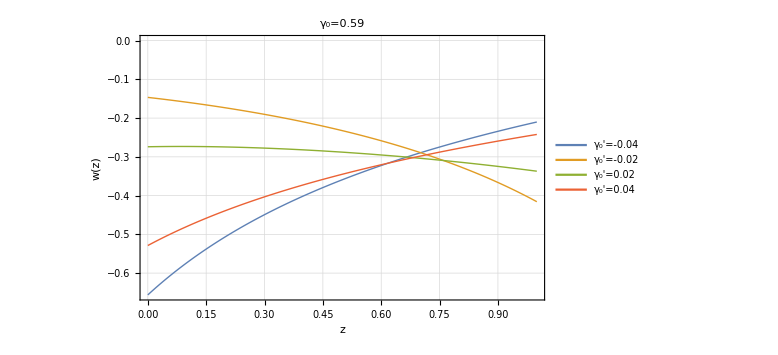

```mathematica
list4=ListLinePlot[{points1,points2,points3, points4}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["w(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_0'=-0.04", "γ_0'=-0.02", "γ_0'=0.02", "γ_0'=0.04"},LegendFunction->"Frame", Background->White],{Right,Bottom}], GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["γ_0=0.59", Black, FontSize->20]]
```

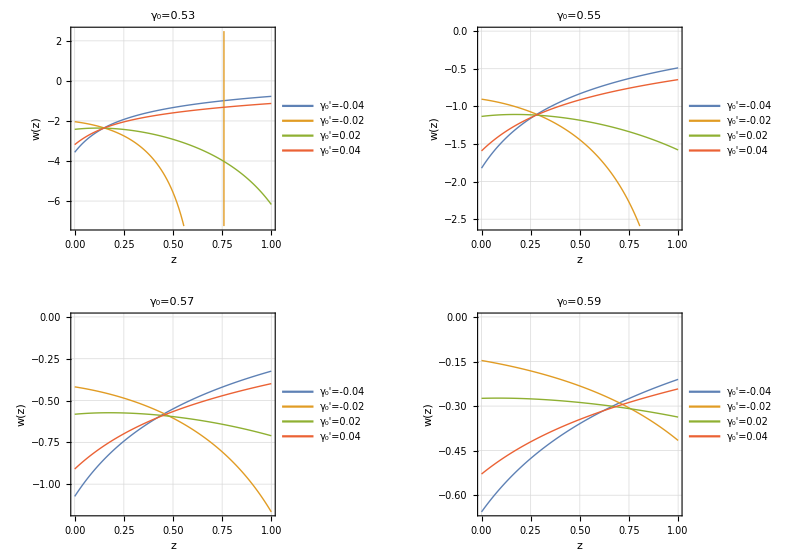

```mathematica
graph=GraphicsGrid[{{list,list2}, {list3, list4}}, ImageSize->Full, Spacings->20]
```

```mathematica
SetDirectory["C:\\Users\\Gerald\\Desktop\\7sem\\dark energy\\final_plots"]
```

C:\Users\Gerald\Desktop\7sem\dark energy\final_plots

```mathematica
Export["w(z)_gamma0.png",graph,ImageResolution->500]
```

w(z)_gamma0.png